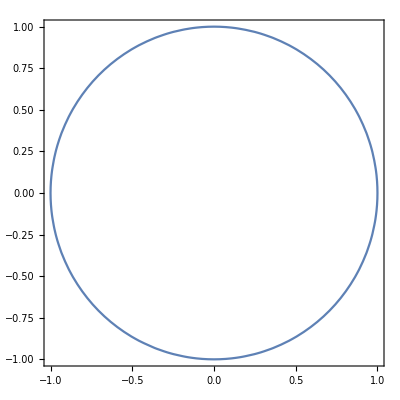

```mathematica
ContourPlot[{x^2+y^2==1},{x,-1,1},{y,-1,1}]
```

```mathematica
Plot[Table[BesselJ[n,x],{n,5}],{x,0,15}]
```

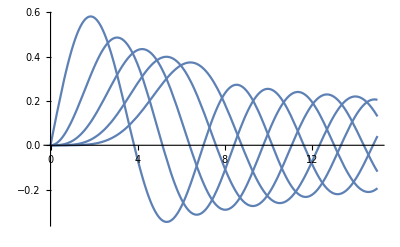

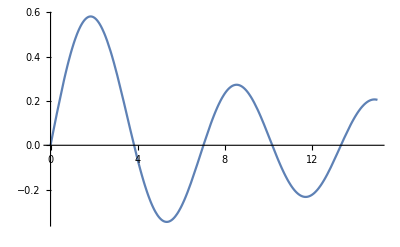

```mathematica
Plot[BesselJ[1,x],{x,0,15}]
```

```mathematica
Subscript[2, 2]*2
2^2*2
```

2 2_2

8

```mathematica
Subscript[n, 1]=1.003(*芯层*)
Subscript[n, 2]=1(*包层*)
λ=1550*10^-9(*波长*)
Subscript[k, 0]=2*Pi/λ(*波数*)
ContourPlot[{BesselJ[1,sqrt[Subscript[k, 0]^2*Subscript[n, 1]^2-β^2]*a]/(sqrt[Subscript[k, 0]^2*Subscript[n, 1]^2-β^2]*a*BesselJ[0,sqrt[Subscript[k, 0]^2*Subscript[n, 1]^2-β^2]*a])== -BesselK[1,sqrt[-Subscript[k, 0]^2*Subscript[n, 2]^2+β^2]*a]/(sqrt[-Subscript[k, 0]^2*Subscript[n, 2]^2+β^2]*a*BesselK[0,sqrt[-Subscript[k, 0]^2*Subscript[n, 2]^2+β^2]*a])},{a,0,40*10^-6},{β,Subscript[k, 0]*Subscript[n, 2], Subscript[k, 0]*Subscript[n, 1]}]
```

1.003

1

31/20000000

(40000000 π)/31

-Graphics-

```mathematica
sqrt[2]
```

sqrt[2]

```mathematica
Subscript[n, 1]=1.02(*芯层*)
Subscript[n, 2]=1(*包层*)
λ=1550*10^-9(*波长*)
Subscript[k, 0]=2*Pi/λ(*波数*)
ContourPlot[{BesselJ[1,(Subscript[k, 0]^2*Subscript[n, 1]^2-β^2)^0.5*a]/((Subscript[k, 0]^2*Subscript[n, 1]^2-β^2)^0.5*a*BesselJ[0,(Subscript[k, 0]^2*Subscript[n, 1]^2-β^2)^0.5*a])== -BesselK[1,(-Subscript[k, 0]^2*Subscript[n, 2]^2+β^2)^0.5*a]/((-Subscript[k, 0]^2*Subscript[n, 2]^2+β^2)^0.5*a*BesselK[0,(-Subscript[k, 0]^2*Subscript[n, 2]^2+β^2)^0.5*a])},{a,0,9*10^-6},{β,Subscript[k, 0]*Subscript[n, 2], Subscript[k, 0]*Subscript[n, 1]}]
```

1.02

1

31/20000000

(40000000 π)/31

-Graphics-

1.003

1

31/20000000

(40000000 π)/31

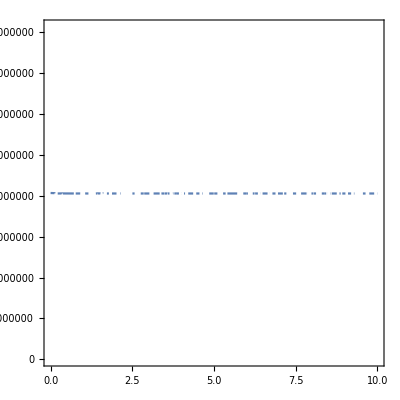

```mathematica
Subscript[n, 1]=1.003(*芯层*)
Subscript[n, 2]=1(*包层*)
λ=1550*10^-9(*波长*)
Subscript[k, 0]=2*Pi/λ(*波数*)
ContourPlot[{BesselJ[1,(Subscript[k, 0]^2*Subscript[n, 1]^2-β^2)^0.5*a]== -BesselK[1,(-Subscript[k, 0]^2*Subscript[n, 2]^2+β^2)^0.5*a]},{a,0,10},{β,0, Subscript[k, 0]*Subscript[n, 1]*2}]
```

```mathematica
Subscript[n, 1]=1.02(*芯层*)
Subscript[n, 2]=1(*包层*)
λ=1550*10^-9(*波长*)
Subscript[k, 0]=2*Pi/λ(*波数*)
Show@Region@ParametricRegion[{{a,β},BesselJ[1,h a]/(h a BesselJ[0,h a])==-BesselK[1,q a]/(q a BesselK[0,q a])&&Subscript[k, 0]^2 Subscript[n, 1]^2==β^2 + h^2 && Subscript[k, 0]^2 Subscript[n, 2]^2 + q^2==β^2 },{a,β,h,q}]
```

1.02

1

31/20000000

(40000000 π)/31

RegionPlot::nnregion: ParametricRegion[{{a,β},BesselJ[1,a h]/(BesselJ[0,Times[«2»]] a h)==-BesselK[1,a q]/(BesselK[0,Times[«2»]] a q)&&1.70961×10^13==β^2+h^2&&(1600000000000000 π^2)/961+q^2==β^2},{a,β,h,q}] cannot be automatically discretized.

RegionPlot::invplotreg: {ParametricRegion[{{a,β},BesselJ[1,Times[«2»]]/(BesselJ[«2»] a h)==-BesselK[1,Times[«2»]]/(BesselK[«2»] a q)&&1.70961×10^13==β^2+h^2&&1600000000000000/961 Power[«2»]+q^2==β^2},{a,β,h,q}]} is not a valid region to plot.

RegionPlot::nnregion: ParametricRegion[{{a,β},BesselJ[1,a h]/(BesselJ[0,Times[«2»]] a h)==-BesselK[1,a q]/(BesselK[0,Times[«2»]] a q)&&1.70961×10^13==β^2+h^2&&(1600000000000000 π^2)/961+q^2==β^2},{a,β,h,q}] cannot be automatically discretized.

RegionPlot::invplotreg: {ParametricRegion[{{a,β},BesselJ[1,Times[«2»]]/(BesselJ[«2»] a h)==-BesselK[1,Times[«2»]]/(BesselK[«2»] a q)&&1.70961×10^13==β^2+h^2&&1600000000000000/961 Power[«2»]+q^2==β^2},{a,β,h,q}]} is not a valid region to plot.

RegionPlot::argr: RegionPlot called with 1 argument; 3 arguments are expected.

RegionPlot::nnregion: ParametricRegion[{{a,β},BesselJ[1,a h]/(BesselJ[0,Times[«2»]] a h)==-BesselK[1,a q]/(BesselK[0,Times[«2»]] a q)&&1.70961×10^13==β^2+h^2&&(1600000000000000 π^2)/961+q^2==β^2},{a,β,h,q}] cannot be automatically discretized.

General::stop: Further output of RegionPlot::nnregion will be suppressed during this calculation.

RegionPlot::invplotreg: {ParametricRegion[{{a,β},BesselJ[1,Times[«2»]]/(BesselJ[«2»] a h)==-BesselK[1,Times[«2»]]/(BesselK[«2»] a q)&&1.70961×10^13==β^2+h^2&&1600000000000000/961 Power[«2»]+q^2==β^2},{a,β,h,q}]} is not a valid region to plot.

General::stop: Further output of RegionPlot::invplotreg will be suppressed during this calculation.

RegionPlot::argr: RegionPlot called with 1 argument; 3 arguments are expected.

General::stop: Further output of RegionPlot::argr will be suppressed during this calculation.

```mathematica
RegionPlot[ParametricRegion[{{a,β},BesselJ[1,a h]/(BesselJ[0,a h] a h)==-BesselK[1,a q]/(BesselK[0,a q] a q)&&1.7096085608979594*^13==β^2+h^2&&(1600000000000000 π^2)/961+q^2==β^2},{a,β,h,q}],{}]
```

RegionPlot::nnregion: ParametricRegion[{{a,β},BesselJ[1,a h]/(BesselJ[0,Times[«2»]] a h)==-BesselK[1,a q]/(BesselK[0,Times[«2»]] a q)&&1.70961×10^13==β^2+h^2&&(1600000000000000 π^2)/961+q^2==β^2},{a,β,h,q}] cannot be automatically discretized.

RegionPlot::invplotreg: {ParametricRegion[{{a,β},BesselJ[1,Times[«2»]]/(BesselJ[«2»] a h)==-BesselK[1,Times[«2»]]/(BesselK[«2»] a q)&&1.70961×10^13==β^2+h^2&&1600000000000000/961 Power[«2»]+q^2==β^2},{a,β,h,q}]} is not a valid region to plot.

RegionPlot::nnregion: ParametricRegion[{{a,β},BesselJ[1,a h]/(BesselJ[0,Times[«2»]] a h)==-BesselK[1,a q]/(BesselK[0,Times[«2»]] a q)&&1.70961×10^13==β^2+h^2&&(1600000000000000 π^2)/961+q^2==β^2},{a,β,h,q}] cannot be automatically discretized.

RegionPlot::invplotreg: {ParametricRegion[{{a,β},BesselJ[1,Times[«2»]]/(BesselJ[«2»] a h)==-BesselK[1,Times[«2»]]/(BesselK[«2»] a q)&&1.70961×10^13==β^2+h^2&&1600000000000000/961 Power[«2»]+q^2==β^2},{a,β,h,q}]} is not a valid region to plot.

RegionPlot::argr: RegionPlot called with 1 argument; 3 arguments are expected.

```mathematica
RegionPlot[ParametricRegion[{{a,β},BesselJ[1,a h]/(BesselJ[0,a h] a h)==-BesselK[1,a q]/(BesselK[0,a q] a q)&&1.7096085608979594*^13==β^2+h^2&&(1600000000000000 π^2)/961+q^2==β^2},{a,β,h,q}],{a,0,40*10^-6},{β,Subscript[k, 0]*Subscript[n, 2], Subscript[k, 0]*Subscript[n, 1]}]
```

ImplicitRegion::bcond: ParametricRegion[{{a,β},BesselJ[1,a h]/(BesselJ[0,Times[«2»]] a h)==-BesselK[1,a q]/(BesselK[0,Times[«2»]] a q)&&1.70961×10^13==β^2+h^2&&(1600000000000000 π^2)/961+q^2==β^2},{a,β,h,q}] should be a Boolean combination of equations, inequalities, and Element statements.

-Graphics-